```mathematica
Quit[];
```

```mathematica
Get@FileNameJoin@{NotebookDirectory[],"Include.m"};
$DataFolder="D:\\Data";
Include/@{"Data.nb"};
```

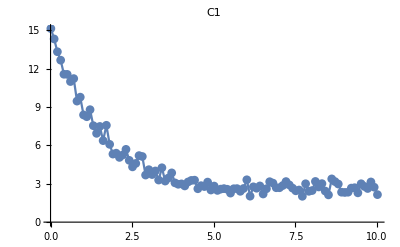
{0.12217,-Graphics-}

```mathematica
Quiet[ImportData@"TimeScan-20180621174840"=.;];
AbsoluteTiming[
DataPlot["TimeScan-20180621174840",C1]
]
```

```mathematica
Quiet[ImportData@"Test-20180624190631"=.;];
AbsoluteTiming[
DataPlot["Test-20180624190631",C1]
]
```

{0.0292817,-Graphics-}

```mathematica
data=ImportData@"TimeScan-20180621174840";
path="Test-20180624190631";
ExportData[path,CountsToXY@data];
```

```mathematica
(*data=Import@DataPath@path;
ExportData[path,{"X_Range"->{{50,0,-1}},"Y_Wavelength"->(List/@data⟦1,All,1⟧),"Y_AverageCount"->(List/@data⟦1,All,2⟧)}];
*)
```

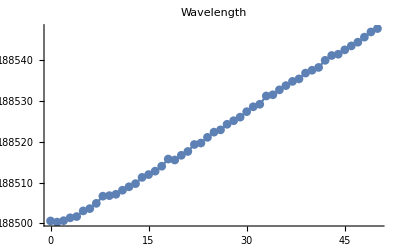

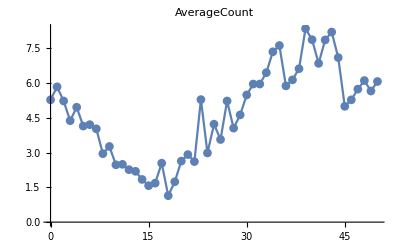

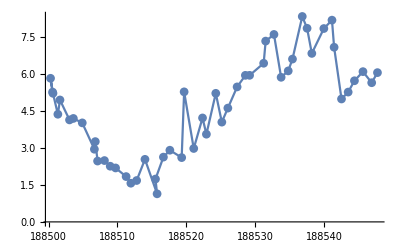

```mathematica
path="WL935-20180621182000";
data=ImportData@path;
DataPlot[data,"Wavelength"]
DataPlot[data,"AverageCount"]
DataPlot[Last/@LoadXY[data,{"Wavelength","AverageCount"}]]
```

```mathematica
3*^8/369.526232-3*^8/369.526242
```

0.02197

```mathematica
3*^8/369.526228-3*^8/369.526242
```

0.030758

```mathematica
<<"D:\\app\\LabVIEW\\LabVIEW.m";
```

```mathematica
sequencer=GetAllCtrls@"D:\\LabVIEW\\Sequencer.min\\Sequencer.min.vi";
sequencerData=sequencer@"Edit.Sequence.Data";
sequencerCounts=sequencer@"Counts";
```

```mathematica
SequencerData[]:=(CtrlSignalValue[sequencerData,True];
While[CtrlGetValue[sequencerData]===True,Null];
Partition[CtrlGetValue@sequencerCounts,4]);
```

```mathematica
Dynamic@ListLinePlot[data,PlotMarkers->Automatic]
```

```mathematica
data={};
stop=False;
PrintTemporary@Button["STOP",stop=True];
Do[If[stop,Break[]];SetPIDCourseNum[3,ToString@SetAccuracy[935+1*^-6w,7]];
Pause[0.1];AppendTo[data,{1*^6(GetWavelengthNum[3]-935),Mean@N@SequencerData[]⟦All,1⟧}],{w,188500,188550}];
```

```mathematica
data={};
stop=False;
PrintTemporary@Button["STOP",stop=True];
Do[If[stop,Break[]];SetPIDCourseNum[1,ToString@SetAccuracy[369+1*^-6w,7]];
Pause[0.1];AppendTo[data,{1*^6(GetWavelengthNum[1]-369),Mean@N@SequencerData[]⟦All,1⟧}],{w,526290,526220,-1}];
w=526260;
SetPIDCourseNum[1,ToString@SetAccuracy[369+1*^-6w,7]];
```

```mathematica
Needs@"NETLink`";
```

```mathematica
GetDeviationMode=DefineDLLFunction["GetDeviationMode","wlmData.dll","bool",{"bool"}];
SetDeviationMode=DefineDLLFunction["SetDeviationMode","wlmData.dll","long",{"bool"}];
GetWavelengthNum=DefineDLLFunction["GetWavelengthNum","wlmData.dll","double",{"int"}];
GetPIDCourseNum=DefineDLLFunction["GetPIDCourseNum","wlmData.dll","long",{"long","char[]"}];
SetPIDCourseNum=DefineDLLFunction["SetPIDCourseNum","wlmData.dll","long",{"long","const char*"}];
```

```mathematica
GetDeviationMode[False]
```

False

```mathematica
buf=MakeNETObject[ConstantArray[0,64],"System.SByte[]"];
GetPIDCourseNum[3,buf];
StringTrim@FromCharacterCode@NETObjectToExpression@buf
ReleaseNETObject@buf;
```

935.188540.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
SetPIDCourseNum[3,"935.188540"]
```

0